```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ken_l/Documents/active-ads/images

```mathematica
Options[Graph]
```

{AlignmentPoint→Center,AnnotationRules→{},AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ContentSelectable→Automatic,DirectedEdges→Automatic,EdgeCapacity→Automatic,EdgeCost→Automatic,EdgeLabels→None,EdgeLabelStyle→Automatic,EdgeShapeFunction→Automatic,EdgeStyle→Automatic,EdgeWeight→Automatic,Editable→False,Epilog→{},FormatType→TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→None,FrameTicksStyle→{},GraphHighlight→{},GraphHighlightStyle→Automatic,GraphLayout→Automatic,GraphRoot→Automatic,GraphStyle→Automatic,GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,LabelStyle→{},PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme→Automatic,Prolog→{},Properties→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{},VertexCapacity→Automatic,VertexCoordinates→Automatic,VertexLabels→None,VertexLabelStyle→Automatic,VertexShape→Automatic,VertexShapeFunction→Automatic,VertexSize→Automatic,VertexStyle→Automatic,VertexWeight→Automatic}

## First color me graph

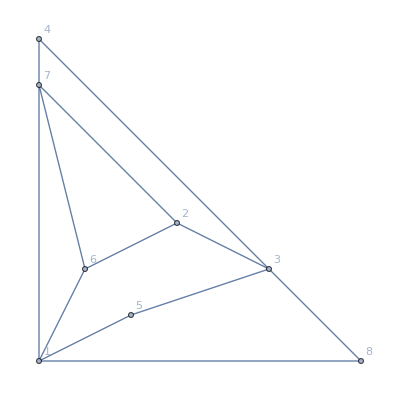

```mathematica
SeedRandom[30];
G=RandomGraph[{8,12}]//Graph[#,GraphLayout->"PlanarEmbedding",VertexLabels->"Name",VertexLabelStyle->Larger]&
```

```mathematica
p=ChromaticPolynomial[G]
```

x↦x^8-12 x^7+64 x^6-198 x^5+382 x^4-453 x^3+300 x^2-84 x

```mathematica
p/@Range[1,10]
```

{0,0,18,1584,23580,174240,859950,3251808,10171224,27596160}

```mathematica
G//Export["fig-colorme-1.png",#,"PNG"]&
```

fig-colorme-1.png

```mathematica
TableForm[{Range[8],Table["__",{8}]}]//TeXForm
```

\begin{array}{cccccccc}
 1 & 2 & 3 & 4 & 5 & 6 & 7 & 8 \\
 \_\_ & \_\_ & \_\_ & \_\_ & \_\_ &
   \_\_ & \_\_ & \_\_ \\
\end{array}

```mathematica
List@@#&/@EdgeList[G]//StandardForm//Print
```

{{1,5},{1,6},{1,7},{1,8},{2,3},{2,6},{2,7},{3,4},{3,5},{3,8},{4,7},{6,7}}

## Second color me graph

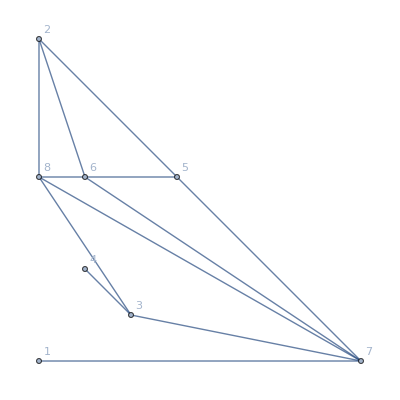

```mathematica
SeedRandom[4];
n=8;G=RandomGraph[{n,12}]//Graph[#,GraphLayout->"PlanarEmbedding",VertexLabels->"Name",VertexLabelStyle->Larger]&
```

```mathematica
ChromaticPolynomial[G][x]//Factor
```

(x-2)^2 (x-1)^3 x (x^2-5 x+7)

```mathematica
p/@Range[1,10]
```

{0,0,24,1296,20160,156000,793800,3062304,9709056,26593920}

```mathematica
G//Export["fig-colorme-2.png",#,"PNG"]&
```

fig-colorme-2.png

```mathematica
TableForm[{Range[n],Table["__",{n}]}]//TeXForm
```

\begin{array}{cccccccc}
 1 & 2 & 3 & 4 & 5 & 6 & 7 & 8 \\
 \_\_ & \_\_ & \_\_ & \_\_ & \_\_ &
   \_\_ & \_\_ & \_\_ \\
\end{array}

```mathematica
List@@#&/@EdgeList[G]//StandardForm//Print
```

{{1,7},{2,5},{2,6},{2,8},{3,4},{3,7},{3,8},{5,6},{5,7},{6,7},{6,8},{7,8}}